# 1-D universal estimator using DNN

Given the pdf of some distribution and a sample containing m observations drawn from dist using pdf with true parameter θ, The UniversalEstimator(pdf, sample, θ) returns  a tuple (Overscript[θ, ^], e, CRB) where Overscript[θ, ^] is the predicted parameter, e is the abs-error | θ - Overscript[θ, ^] | and CRB is the Cramer-Rao-Bound (θ, m) of the distribution with θ.

### Fisher Information

```mathematica
(*Module is to state that {x,y......} inside the [] is local symbol]*)
```

Fisher information for a distribution with a single parameter θ

```mathematica
FisherInformation[dist_]:=Module[{f},
(*let f be the PDF of dist with parameter θ evaluated at x*)
f = PDF[dist[θ],x];
Expectation[D[Log[f], {θ}]^2,x\[Distributed]dist[θ]]  (*the return of this function*)
]
```

### Cramer-Rao bound

Cramer-Rao bound for a single parameter d and m observations

```mathematica
CRB[dist_, d_, m_]:=(
fi=FisherInformation[dist];
FI[θ_]:=Evaluate[fi];
(1/FI[d])/m  (*the return of this function*)
)
```

#### Examples

#### Poisson distribution

```mathematica
FisherInformation@PoissonDistribution
```

1/θ

```mathematica
CRB[PoissonDistribution, 3, 2048]
```

3/2048

#### Geometric distribution

```mathematica
FisherInformation@GeometricDistribution
```

-1/((-1+θ) θ^2)

```mathematica
CRB[GeometricDistribution, 0.5, 2048]
```

0.0000610352

#### Normal distribution

```mathematica
NormalDistribution1D[σ_]:=NormalDistribution[0,σ];
```

```mathematica
FisherInformation@NormalDistribution1D
```

2/θ^2

```mathematica
CRB[NormalDistribution1D, 3, 2048]
```

9/4096

## Generating data (without duplicating θ and logging the histogram)

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for a given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	S: number of samples per θ 
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples: max[samples] or max[samples]+1 (with zero padding)
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, f_, range_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS},
		params=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
		(*generate M different random initparameters in the range [min_θ,max_θ]*) 
		samples=Table[f[params[[i]],n],{i,1,M}];
		(*generate M distributions, each distribution has n number/data*, now we have M*n data*)
		MAXBINS=5000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=HistogramList[x,{0,nbins,1}][[2]]; (*without using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[5,10,f,{2,3}]//TableForm];*)
```

{6,3,0,1}→2.67938
{6,0,4,0}→2.21798
{7,1,1,1}→2.25193
{7,2,1,0}→2.76568
{6,1,1,2}→2.16986

## DNN

Generate a DNN for predicting the parameter θ from the distribution histogram
The input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
LinearLayer[bins],  
BatchNormalizationLayer[],  (*batch normaliztiozion*)
ElementwiseLayer[Ramp], (*Ramp is the relu*)

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using DNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 1024;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->1024
 
];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with DNN

n : number of samples drawn for a given θ 
M : number of different θ generated in the range [min_θ, max_θ]
S : number of samples per θ

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, crb,Var,a},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];
(*define the size of the test set*)
M = 100;
n = 1024;
a = 5;

Θ=Table[a,M]; (*create M distributions of parameter a*)
	
g[θ_,m_] := RandomVariate[dist[θ],m];

samples = Table[g[Θ[[i]], n], {i,1,M,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M,1 }];
(*Compute Cramer-Rao bound at a*)
crb = CRB[dist, a, n];
(*evaluate prediction errors*)
e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M,1 }];
(*Compute the varience of each Subscript[θ, i]*)
Var = Mean[(Θhat-Mean[Θhat])^2];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["Variance for θ:",Var];
Print["crb for θ:",crb];
Print["ratio of variance and crb for θ:",Var/crb];
Print["RMSE:",RootMeanSquare[e]];

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for different distributions

### Poisson distribution

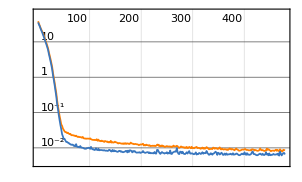
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4790  rounds:479  time:35s  examples/s:143474
data | ,,  training examples:10000  validation examples:5000  processed examples:4904960  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:8.42×10^-3
validation | ,,  loss:6.52×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

θ̂: {5.0374,4.91972,4.91926,5.16316,5.21501,5.13185,4.99966,5.09299,5.05576,4.94257,5.05135,4.85655,5.08734,4.85768,4.86975,5.0152,4.99498,5.06703,4.83784,4.98064,4.92413,4.93343,4.91791,5.05758,5.09029,5.01215,4.88177,5.00744,4.9953,4.98076,5.04468,5.06869,4.84087,4.90404,4.95496,5.11529,5.09756,5.01114,5.0511,5.15669,5.04578,5.04436,5.11171,4.92136,4.95746,5.05274,4.89625,4.97023,5.15916,5.12291,5.01351,4.96597,4.9524,5.02074,4.85664,5.10123,5.09232,4.87037,5.04742,5.12818,5.12751,5.05738,4.87887,4.90178,4.89811,5.07412,5.03847,5.03748,5.12862,4.89557,4.9243,4.99231,4.97012,4.92927,5.04015,4.8517,5.03142,4.92233,4.93307,4.91653,5.04696,4.90404,5.04542,5.02205,5.03826,4.99835,4.95968,4.9792,5.06202,5.01959,5.05703,5.01355,5.10286,4.90338,4.96043,5.005,4.88214,4.91927,4.89696,5.03087}

abs(θ-θ̂): {0.037396,0.0802794,0.0807438,0.163156,0.215005,0.131849,0.000344276,0.0929918,0.0557561,0.0574284,0.0513463,0.143446,0.0873384,0.142319,0.13025,0.0152006,0.00501585,0.0670319,0.162163,0.0193596,0.0758672,0.0665731,0.082088,0.0575805,0.0902882,0.0121517,0.118234,0.00744104,0.00470209,0.0192366,0.0446825,0.0686932,0.159129,0.0959563,0.0450401,0.11529,0.0975585,0.011138,0.0510974,0.156693,0.045783,0.0443649,0.111711,0.0786395,0.0425363,0.052743,0.103753,0.0297661,0.159155,0.122914,0.0135074,0.0340252,0.0476031,0.0207391,0.143361,0.101235,0.0923185,0.129627,0.04742,0.12818,0.127507,0.0573802,0.121131,0.0982199,0.101892,0.074122,0.038466,0.0374823,0.128622,0.104428,0.0757003,0.00769281,0.0298753,0.0707259,0.0401521,0.148301,0.0314198,0.0776653,0.066927,0.0834703,0.0469642,0.0959611,0.0454178,0.0220542,0.0382581,0.00165415,0.0403228,0.0208025,0.0620213,0.0195913,0.0570345,0.0135512,0.102865,0.0966234,0.0395713,0.00499725,0.117862,0.0807276,0.103042,0.0308728}

Variance for θ:0.00736024

crb for θ:5/1024

ratio of variance and crb for θ:1.50738

RMSE:0.0858019

```mathematica
{Θ, e} = RunExperiment[PoissonDistribution, {1,10}];
```

### Geometric distribution

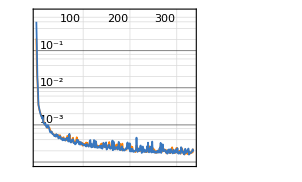
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3350  rounds:335  time:32s  examples/s:108207
data | ,,  training examples:10000  validation examples:5000  processed examples:3430400  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:2.29×10^-4
validation | ,,  loss:1.91×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

θ̂: {0.504276,0.503076,0.499276,0.495436,0.519933,0.482911,0.52381,0.494053,0.534092,0.457714,0.490141,0.493024,0.49324,0.509108,0.526642,0.521482,0.48767,0.509467,0.483409,0.50214,0.479821,0.504416,0.496563,0.493518,0.515121,0.487471,0.502754,0.50819,0.50584,0.521344,0.474741,0.485509,0.5165,0.49333,0.500534,0.4998,0.506207,0.508451,0.497343,0.48016,0.488648,0.483798,0.490872,0.492681,0.51151,0.485088,0.49849,0.496241,0.496016,0.503397,0.507582,0.467885,0.512846,0.517358,0.528892,0.514003,0.494486,0.483538,0.529738,0.5029,0.526149,0.489097,0.505776,0.487426,0.50511,0.482177,0.520604,0.507717,0.503879,0.522264,0.505404,0.496982,0.506425,0.492939,0.501186,0.478088,0.488752,0.518327,0.494457,0.490066,0.493286,0.487746,0.512765,0.504559,0.50966,0.501959,0.49617,0.507379,0.495561,0.487856,0.506722,0.484576,0.494621,0.49165,0.511949,0.510017,0.491281,0.486418,0.506718,0.493838}

abs(θ-θ̂): {0.00427622,0.00307626,0.000724256,0.00456375,0.019933,0.0170887,0.0238099,0.00594705,0.0340922,0.0422858,0.00985911,0.00697604,0.00675958,0.00910765,0.0266415,0.0214821,0.0123303,0.00946689,0.0165911,0.00214022,0.0201788,0.00441629,0.00343734,0.00648203,0.0151206,0.0125287,0.00275403,0.00818998,0.00583982,0.0213441,0.0252587,0.0144907,0.0164998,0.00666976,0.000534415,0.000199646,0.00620663,0.00845081,0.002657,0.0198397,0.0113521,0.0162021,0.00912753,0.00731909,0.0115095,0.0149117,0.00150976,0.00375909,0.00398389,0.00339741,0.00758207,0.0321146,0.0128463,0.0173575,0.0288924,0.0140032,0.00551435,0.0164621,0.0297381,0.00289959,0.026149,0.0109031,0.00577646,0.0125744,0.00510991,0.0178227,0.0206035,0.00771725,0.00387949,0.0222638,0.00540441,0.00301787,0.00642484,0.00706083,0.00118649,0.0219116,0.0112478,0.0183265,0.00554252,0.00993443,0.00671446,0.0122544,0.0127652,0.00455934,0.00965971,0.00195938,0.00383043,0.00737917,0.00443861,0.0121439,0.00672179,0.015424,0.00537935,0.00835016,0.0119488,0.0100165,0.00871873,0.0135821,0.0067184,0.00616184}

Variance for θ:0.000192879

crb for θ:0.00012207

ratio of variance and crb for θ:1.58006

RMSE:0.0138881

```mathematica
{Θ, e} = RunExperiment[GeometricDistribution, {0.2,0.8}];
```